## Riemann problems

## Setup

### working directory

```mathematica
wd=SetDirectory@NotebookDirectory[]
root=ParentDirectory[ParentDirectory[wd]]
```

/Users/Lipei/Documents/GitHub/BEShydro/tests/Plotting

/Users/Lipei/Documents/GitHub/BEShydro

### plot styles

```mathematica
styles={Directive[RGBColor[0,0,0],AbsoluteThickness[4]],Directive[RGBColor[0.9,0,0],AbsoluteThickness[3],AbsoluteDashing[Medium]],Directive[RGBColor[0,0,0.5],AbsoluteThickness[3],AbsoluteDashing[{10,5}]],Directive[RGBColor[0,0.5,0],AbsoluteThickness[3],AbsoluteDashing[{10,5,2,5}]],Directive[RGBColor[1,0.5,0.0],AbsoluteThickness[3],AbsoluteDashing[{1,4}]],Directive[RGBColor[0.5,0.5,0.5],AbsoluteThickness[2],AbsoluteDashing[{1,4}]]};
```

```mathematica
FrameTicksFontSize=30;
FrameFontSize=30;PlotOptions={Axes->False,Frame->True,FrameTicksStyle->{Directive[FontSize->FrameTicksFontSize,FontFamily->"Times"],Directive[FontSize->FrameTicksFontSize,FontFamily->"Times"]},FrameStyle->{Directive[AbsoluteThickness[1.1]],Directive[AbsoluteThickness[1.1]]},BaseStyle->{FontFamily->"Times",FontSize->30},AspectRatio->0.75,ImageSize->600,PlotRange->All};
SetOptions[Plot,PlotOptions];
SetOptions[LogPlot,PlotOptions];
SetOptions[LogLogPlot,PlotOptions];
SetOptions[LogLinearPlot,PlotOptions];
SetOptions[ListPlot,PlotOptions];
SetOptions[PolarPlot,PlotOptions];
```

### data reader

```mathematica
Off[Interpolation::inhr];
varInt[t_,dir_,var_]:=Interpolation[Import[dir<>"/"<>var<>"_"<>ToString[PaddedForm[t,{4,3},NumberPadding->{"","0"}]]<>".dat"],InterpolationOrder->3]
```

## Relativistic Sod shock-tube with Conformal EoS - I. expanding into vacuum

```mathematica
tlist={0.0001,2,4,8};
clist={Black,Red,Blue,Darker[Green]};
```

### analytic result

#### initial condition

```mathematica
e0=15;(*GeV/fm^3*)
n0=10;
cs2=1/3;
cs=Sqrt[cs2];
lim=10;
hbarc=0.197326938;
```

#### analytic solution

```mathematica
e[t_,x_]:=Module[{zeta},zeta=x/t;
If[zeta<-cs,Return[e0]];If[zeta>-cs&&zeta<1,Return[e0*((1-cs)/(1+cs)*(1-zeta)/(1+zeta))^((1+cs2)/(2cs))]];Return[0];]
ux[t_,x_]:=Tanh[-cs/(1+cs2)Log[e[t,x]/e0]];
```

#### make plots

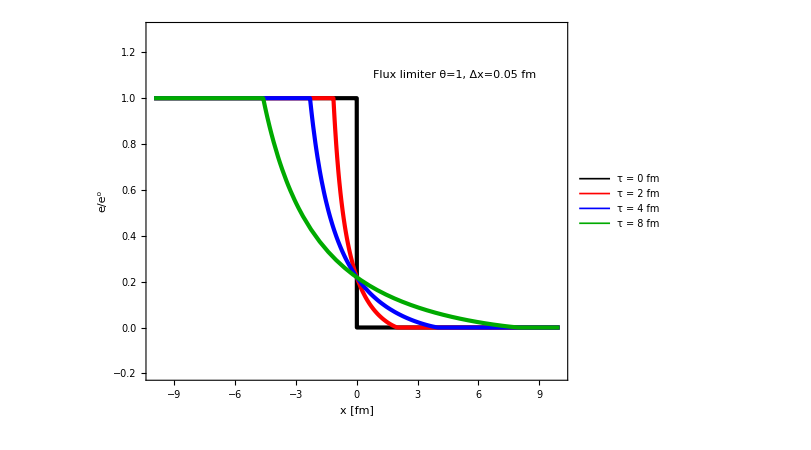

```mathematica
edPlot=Show[Plot[{e[0.0001,x]/e0,e[2,x]/e0,e[4,x]/e0,e[8,x]/e0},{x,-lim,lim},PlotRange->{{-10,10},{-0.2,1.3}},PlotStyle->{{Black,Thickness[0.005]},{Red,Thickness[0.005]},{Blue,Thickness[0.005]},{Darker[Green],Thickness[0.005]}},PlotLegends->Placed[LineLegend[{"τ = 0 fm","τ = 2 fm","τ = 4 fm","τ = 8 fm"},LabelStyle->{FontFamily->"Times",FontSize->20},LegendMarkerSize->{{30,10}}],{.75,0.6}]],FrameLabel->{"x [fm]","e/e^0"},Epilog->Inset["Flux limiter θ=1, Δx=0.05 fm",{4.8,1.1},BaseStyle->{FontFamily->"Times",FontSize->20}],ImageSize->600]
```

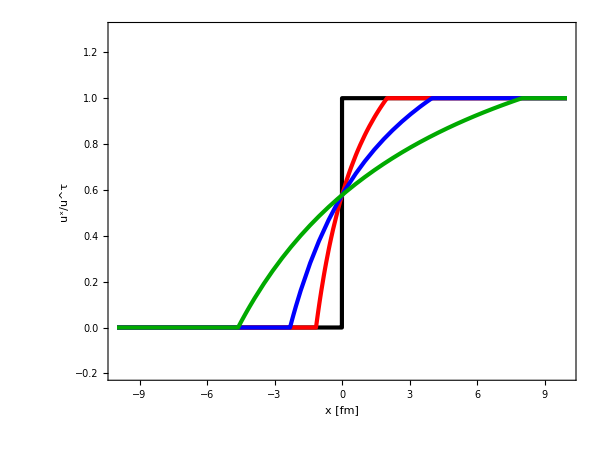

```mathematica
uxPlot=Show[Table[Plot[{ux[tlist[[i]],x]},{x,-lim,lim},PlotRange->{{-10,10},{-0.2,1.3}},PlotStyle->{{AbsoluteThickness[3],clist[[i]]}},PlotLegends->Placed[LineLegend[{tlist[[i]]" fm"},LabelStyle->{FontFamily->"Times",FontSize->20},LegendMarkerSize->{{30,10}}],{.55,0.9}]],{i,1,Length[tlist]}],FrameLabel->{"x [fm]","u^x/u^τ"},ImageSize->600]
```

## Relativistic Sod shock-tube with Conformal EoS - II. expanding into dilute matter

```mathematica
tlist={0.0001,8};
clist={Black,Red,Blue,Darker[Green]};
```

### analytic result [PRC 98,035201 (2018)]

#### initial condition

```mathematica
pR=0.0625;
nR=0.125;
pL=1.0;
nL=1.0;
cs2=1/3;
cs=Sqrt[cs2];
lim=10;
hbarc=0.197326938;
```

#### analytic solution

```mathematica
pC=0.247;
betaC=0.541;
betaL=0;
betaShock=0.785;
betaR=0;
nStar[zeta_]:=nL*((1-cs)/(1+cs)*(1-zeta)/(1+zeta))^(√3/2);
pStar[zeta_]:=pL*((1-cs)/(1+cs)*(1-zeta)/(1+zeta))^(2/√3);
betaStar[zeta_]:=(cs+zeta)/(1+cs*zeta);
nI=nL*(pC/pL)^(3/4);
nII=nR*√((pC(pR+3pC))/(pR(pC+3pR)));
zH[t_]:=-cs*t;
zT[t_]:=((betaC-cs)/(1-betaC*cs))t;
zC[t_]:=betaC*t;
zS[t_]:=betaShock*t;
```

```mathematica
n[t_,x_]:=Module[{zeta},zeta=x/t;
If[x<zH[t],Return[nL]];
If[x>zH[t]&&x<zT[t],Return[nStar[zeta]]];
If[x>zT[t]&&x<zC[t],Return[nI]];
If[x>zC[t]&&x<zS[t],Return[nII]];
Return[nR];]
beta[t_,x_]:=Module[{zeta},zeta=x/t;
If[x<zH[t],Return[betaL]];
If[x>zH[t]&&x<zT[t],Return[betaStar[zeta]]];
If[x>zT[t]&&x<zS[t],Return[betaC]];
If[x>zS[t],Return[betaR]];]
p[t_,x_]:=Module[{zeta},zeta=x/t;
If[x<zH[t],Return[pL]];
If[x>zH[t]&&x<zT[t],Return[pStar[zeta]]];
If[x>zT[t]&&x<zS[t],Return[pC]];
If[x>zS[t],Return[pR]];]
```

#### make plots

```mathematica
pPlot=Show[Plot[{p[0.0001,x],p[8,x]},{x,-lim,lim},PlotRange->Full,PlotStyle->{{Black,AbsoluteThickness[2],DotDashed},{Blue,AbsoluteThickness[6],Opacity[0.3]}},PlotLegends->Placed[LineLegend[{"Initial profile"},LabelStyle->{FontFamily->"Times"},LegendMarkerSize->{{30,10}}],{.75,0.6}]],FrameLabel->{"x [fm]","𝒫_0 [fm^-4]"},Epilog->Inset["(a)",{9,0.95}],ImageSize->600,AspectRatio->3.5/3,ImagePadding->{{100,10},{80,10}}];
```

```mathematica
nplot=Show[Plot[{n[0.0001,x],n[8,x]},{x,-lim,lim},PlotRange->Full,PlotStyle->{{Black,AbsoluteThickness[2],DotDashed},{Darker[Green],AbsoluteThickness[6],Opacity[0.3]}}],FrameLabel->{"x [fm]","𝒩 [fm^-3]"},Epilog->Inset["Flux limiter θ_f=1\n Δx=0.05 fm",{5,0.65},BaseStyle->{FontFamily->"Times"}],ImageSize->600];
plot=Graphics[Text["(b)",{9,0.95}],BaseStyle->{FontFamily->"Times",FontSize->30}];
nPlot=Show[nplot,plot,ImageSize->600,AspectRatio->3.5/3,ImagePadding->{{100,10},{80,10}}];
```

```mathematica
uxPlot=Show[Plot[{beta[0.0001,x],beta[8,x]},{x,-lim,lim},PlotRange->Full,PlotStyle->{{Black,AbsoluteThickness[2],Dashed},{Red,AbsoluteThickness[6],Opacity[0.3]}}],FrameLabel->{"x [fm]","u^x/u^τ"},BaseStyle->{FontFamily->"Times",FontSize->30},Epilog->Inset["(c)",{9,0.52}],ImageSize->600,AspectRatio->3.5/3,ImagePadding->{{100,10},{80,10}}];
```

### numerical data (t_0=0.5fm, dx=0.05 fm dt=0.01fm, and \theta=1)

```mathematica
tlist={8.5};
t0=0.5;
outputDir=root<>"/output";
MapThread[Table[#1[i-1]=varInt[tlist[[i]],outputDir,#2],{i,1,Length[tlist]}]&,{{pInt,uxInt,utInt,nInt},{"p","ux","ut","rhob"}}];
```

### make plots

```mathematica
uxnPlot=Plot[uxInt[0][x,0,0]/utInt[0][x,0,0],{x,-lim,lim},PlotStyle->{Red,AbsoluteThickness[3],Dashing[Large]},ImageSize->600,AspectRatio->3.5/3,ImagePadding->{{100,10},{80,10}}];
pnPlot=Plot[pInt[0][x,0,0],{x,-lim,lim},PlotStyle->{Blue,AbsoluteThickness[3],Dashing[Large]},ImageSize->600,AspectRatio->3.5/3,ImagePadding->{{100,10},{80,10}}];
nnPlot=Plot[nInt[0][x,0,0],{x,-lim,lim},PlotStyle->{Darker[Green],AbsoluteThickness[3],Dashing[Large]},ImageSize->600,AspectRatio->3.5/3,ImagePadding->{{100,10},{80,10}}];
pCompare=Show[pPlot,pnPlot];
uxCompare=Show[uxPlot,uxnPlot];
nCompare=Show[nPlot,nnPlot];
```

```mathematica
Export["Riemann_Conformal_p.pdf",pCompare,ImageResolution->200]
Export["Riemann_Conformal_ux.pdf",uxCompare,ImageResolution->200]
Export["Riemann_Conformal_n.pdf",nCompare,ImageResolution->200]
```

Riemann_Conformal_p.pdf

Riemann_Conformal_ux.pdf

Riemann_Conformal_n.pdf

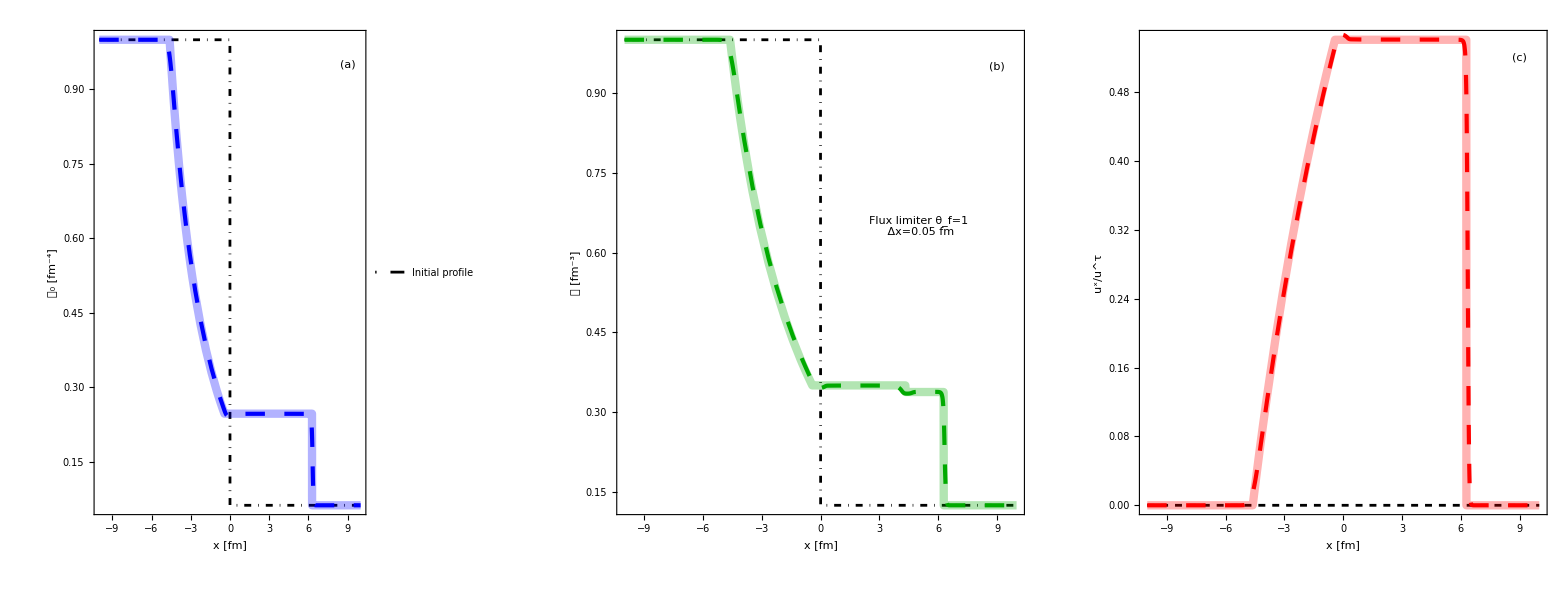

```mathematica
RiemannTest=GraphicsGrid[{{pCompare,nCompare,uxCompare}},Spacings->{0, -45},ImageSize->1800]
```

```mathematica
Export["Riemann_test.pdf",RiemannTest,ImageResolution->200]
```

Riemann_test.pdf

## Relativistic Sod shock-tube with Non-conformal EoS - Baryon density

```mathematica
tlist={8.5};
t0=0.5;
outputDir=wd<>"/Riemann_NonConformalEoS";
MapThread[Table[#1[i-1]=varInt[tlist[[i]],outputDir,#2],{i,1,Length[tlist]}]&,{{pInt,uxInt,utInt,nInt},{"p","ux","ut","rhob"}}];
```

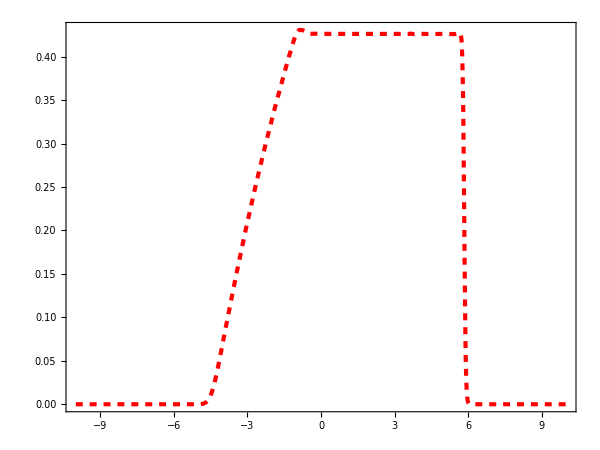

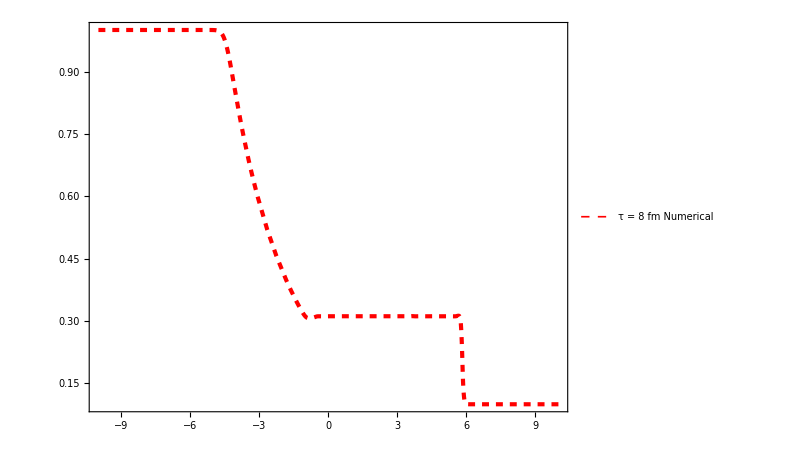

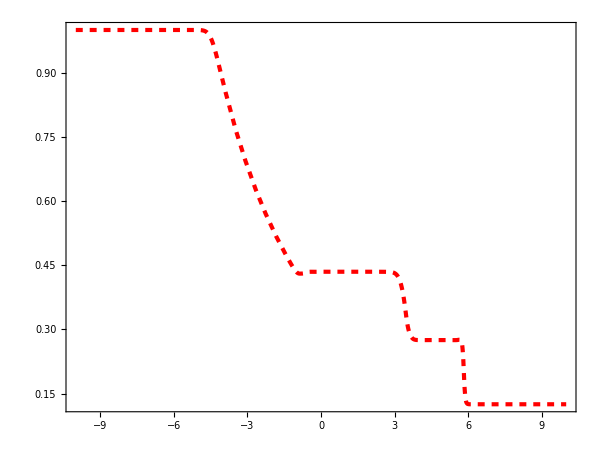

```mathematica
uxnPlot=Plot[uxInt[0][x,0,0]/utInt[0][x,0,0],{x,-10,10},PlotStyle->{Red,Thickness[0.005],Dashed}]
pnPlot=Plot[pInt[0][x,0,0],{x,-10,10},PlotStyle->{Red,Thickness[0.005],Dashed},PlotLegends->Placed[LineLegend[{"τ = 8 fm Numerical"},LabelStyle->{FontFamily->"Times",FontSize->20},LegendMarkerSize->{{30,10}}],{.75,0.6}]]
nnPlot=Plot[nInt[0][x,0,0],{x,-10,10},PlotStyle->{Red,Thickness[0.005],Dashed}]
```

```mathematica
Export["pCompare_Riemann_NonConformal.pdf",uxnPlot,ImageResolution->200]
Export["uxCompare_Riemann_NonConformal.pdf",pnPlot,ImageResolution->200]
Export["nCompare_Riemann_NonConformal.pdf",nnPlot,ImageResolution->200]
```

pCompare_Riemann_NonConformal.pdf

uxCompare_Riemann_NonConformal.pdf

nCompare_Riemann_NonConformal.pdf